# Cross Polytope

### Author

Eric W. Weisstein
June 12, 2019

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polytopes/CrossPolytope.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/CrossPolytope.html.

©2019 Wolfram Research, Inc. except for portions noted otherwise

## Vertices

```mathematica
(* section 13.4 of Coxeter's Regular Polytopes *)
CrossPolytopeCoordinates[n_]:=Module[{a,r,k},a=Table[Flatten[Table[Through[{Cos,Sin}[(2 r-1) Pi k/n]],{r,Floor[n/2]}]],{k,2 n}];
If[OddQ[n],Table[Join[a[[k]],{(-1)^k/Sqrt[2]}],{k,2 n}],a]/Sqrt[n]
]
```

```mathematica
TextGrid[Table[{n,CrossPolytopeCoordinates[n]},{n,4}],Dividers->All]
```

1 | {{-1/(√2)},{1/(√2)}}
2 | {{0,1/(√2)},{-1/(√2),0},{0,-1/(√2)},{1/(√2),0}}
3 | {{1/(2 √3),1/2,-1/(√6)},{-1/(2 √3),1/2,1/(√6)},{-1/(√3),0,-1/(√6)},{-1/(2 √3),-1/2,1/(√6)},{1/(2 √3),-1/2,-1/(√6)},{1/(√3),0,1/(√6)}}
4 | {{1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2)},{0,1/2,0,-1/2},{-1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{-1/2,0,-1/2,0},{-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{0,-1/2,0,1/2},{1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/2,0,1/2,0}}

## EdgeLength

```mathematica
Table[EuclideanDistance@@@Subsets[CrossPolytopeCoordinates[n],{2}]//FullSimplify//Union,{n,2,5}]
```

{{1,√2},{1,√2},{1,√2},{1,√2}}

## Region

```mathematica
ConvexHullMesh[CrossPolytopeCoordinates[3]]
```

-Graphics3D-

```mathematica
RegionPlot3D[Norm[{x,y,z},1]≤1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

## Content

```mathematica
RegionMeasure[ConvexHullMesh[CrossPolytopeCoordinates[3]]]
```

2.44949

```mathematica
ConvexHullMesh[CrossPolytopeCoordinates[3]]//InputForm
```

BoundaryMeshRegion[{{0.5, 0.8660254037844386, -0.7071067811865475}, {-0.5, 0.8660254037844386, 
 0.7071067811865475}, {-1., 0., -0.7071067811865475}, {-0.5, -0.8660254037844386, 0.7071067811865475}, 
 {0.5, -0.8660254037844386, -0.7071067811865475}, {1., 0., 0.7071067811865475}}, 
 {Polygon[{{1, 5, 3}, {6, 1, 2}, {5, 1, 6}, {1, 3, 2}, {3, 5, 4}, {5, 6, 4}, {3, 4, 2}, {4, 6, 2}}]}, 
 Method -> {"SeparateBoundaries" -> False}]

```mathematica
1/(√2)^2 Integrate[Boole[Norm[{x,y},1]≤1],{x,y}∈FullRegion[2]]//Timing
```

{0.011669,1}

```mathematica
PolyhedronData["Octahedron","Volume"]
```

(√2)/3

```mathematica
1/(√2)^3 Integrate[Boole[Norm[{x,y,z},1]≤1],{x,y,z}∈FullRegion[3]]//Timing
```

{2.34004,(√2)/3}

```mathematica
RegionMeasure[Octahedron[]]
```

(√2)/3

```mathematica
Norm[{x,y,z,w},1]
```

Abs[w]+Abs[x]+Abs[y]+Abs[z]

```mathematica
1/(√2)^4 Integrate[Boole[Norm[{x,y,z,w},1]≤1],{x,y,z,w}∈FullRegion[4]]//Timing
```

{24.4322,1/6}

```mathematica
Table[2^n/(2^(n/2)n!),{n,10}]
```

{√2,1,(√2)/3,1/6,1/(15 √2),1/90,1/(315 √2),1/2520,1/(11340 √2),1/113400}

## Graph

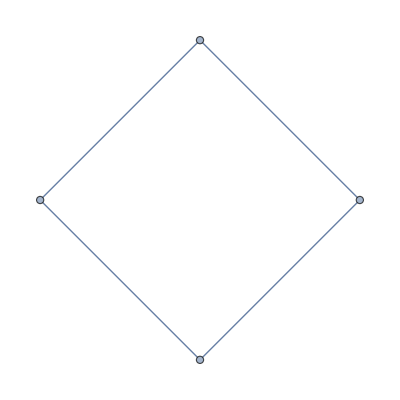
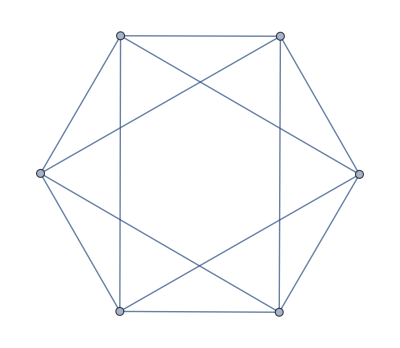
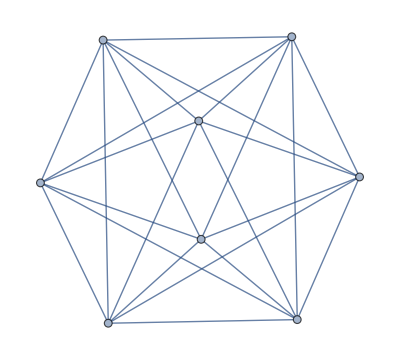
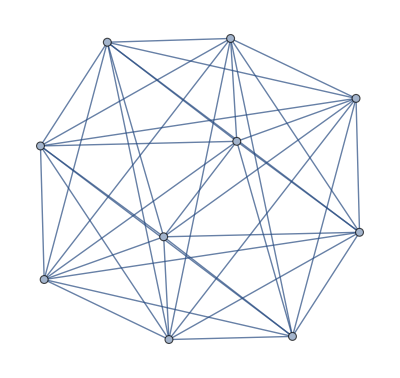
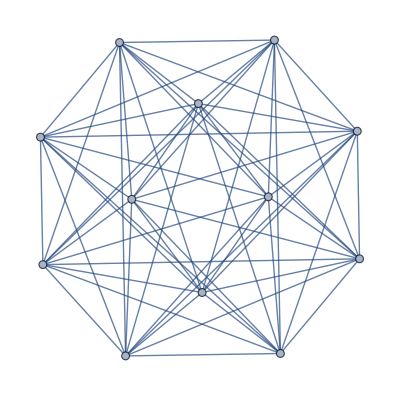

```mathematica
Table[With[{v=CrossPolytopeCoordinates[n]},Graph[UndirectedEdge@@@Select[Subsets[Range[2n],{2}],EuclideanDistance@@v[[#]]==1.&]]],{n,2,6}]
```

```mathematica
RecognizeGraph/@%
```

{SquareGraph,OctahedralGraph,SixteenCellGraph,{CocktailParty,5},{CocktailParty,6}}